```mathematica
Psi0[n_Integer, x_]
```

Psi[n_Integer,x_]

```mathematica
apl[f_]:=(x*f-D[f, x])/Sqrt[2]
```

```mathematica
ami[f_]:=(x*f+D[f, x])/Sqrt[2]
```

```mathematica
solve = DSolve[ami[Psi0[x]]==0,Psi0[x], x]
```

{{Psi0[x]→ⅇ^(-x^2/2) C[1]}}

```mathematica
psi0=Psi0[x]/.solve[[1]]
```

ⅇ^(-x^2/2) C[1]

```mathematica
solve1=Integrate[(psi0)^2,{x, -Infinity, Infinity}]
```

√π C[1]^2

```mathematica
solve2=Solve[solve1==1, C[1]]
```

{{C[1]→-1/π^(1/4)},{C[1]→1/π^(1/4)}}

```mathematica
psi01=psi0/.solve2[[2]]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
psi[0]
```

{ⅇ^(-x^2/2) C[1]}[0]

```mathematica
psi1[0]=psi01
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
psi1[n_]:=Simplify[(apl[psi1[n-1]])/Sqrt[n]]
```

```mathematica
psi1[30]
```

1/(15692092416000 √1077205 π^(1/4))ⅇ^(-x^2/2) (-6190283353629375+185708500608881250 x^2-866639669508112500 x^4+1502175427147395000 x^6-1287578937554910000 x^8+629483036137956000 x^10-190752435193320000 x^12+37731250917360000 x^14-5030833455648000 x^16+460337701824000 x^18-29073960115200 x^20+1258612992000 x^22-36481536000 x^24+673505280 x^26-7127040 x^28+32768 x^30)

```mathematica
norm=NIntegrate[Table[(psi1[k])^2,{k,1,10}],{x, -Infinity, Infinity}](*Численное инт-е*)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

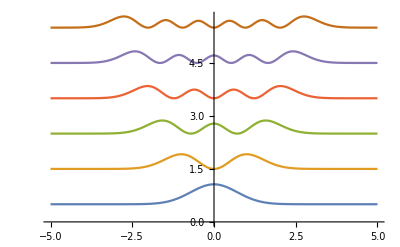

```mathematica
Plot[Evaluate[Table[psi1[p]^2+p+0.5,{p,0,5}]],{x,-5,5}]
```